```mathematica
(* hpc: exterior solution *)
```

```mathematica
rgbss2=(48*y^2)/x^6-(32*w*(y+1/2*v*x^3))/x^3;scalareq=(1-2*y/x)*bph''[x]+(1-(2*y)/x)*(2/(x-2y)*(1-y/x)-(x^2*(w-v))/(x-2y))*bph'[x]+(f2*rgbss2-u2)*bph[x];scalareqex=Simplify[scalareq/.{w->0,v->0,y->ym}];
```

```mathematica
ncpt=1000;ymmin=0.001;ymmax=0.499;f2set={1,2,3,4,5,6,7};u2set={3,5,10,15,20};ymset=Table[0.5-Exp[Log[0.5-ymmin]+(Log[0.5-ymmax]-Log[0.5-ymmin])/(ncpt-1)*(i-1)],{i,1,ncpt}];bphpexset=Table[0,{i,1,ncpt},{jr,1,Length[f2set]},{kr,1,Length[u2set]}];xtail=100;tail=100;
```

```mathematica
Do[bphpshootl=100;bphpshooth=-100;bphpshoottest=bphpshootl;j=0;
While[Abs[bphpshoottest-N[(bphpshootl+bphpshooth)/2]]>10^-6&&j<1000,bphpshoottest=N[(bphpshootl+bphpshooth)/2];scalareqex1=scalareqex/.{ym->ymset[[i]],f2->f2set[[jr]],u2->u2set[[kr]]};
solex=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==bphpshoottest},bph,{x,1,xtail}];tail=bph[x]/.solex[[1]]/.x->xtail;
If[tail>0,bphpshootl=bphpshoottest,bphpshooth=bphpshoottest];j++];bphpexset[[i,jr,kr]]=bphpshoottest,{i,1,ncpt},{jr,1,Length[f2set]},{kr,1,Length[u2set]}]
```

```mathematica
data=Table[{0,0,0,0,0,0,0},{i,1,ncpt}];Do[data[[i,1]]=bphpexset[[i,1,1]],{i,1,ncpt}];Do[data[[i,2]]=bphpexset[[i,2,1]],{i,1,ncpt}];Do[data[[i,3]]=bphpexset[[i,3,1]],{i,1,ncpt}];Do[data[[i,4]]=bphpexset[[i,4,1]],{i,1,ncpt}];Do[data[[i,5]]=bphpexset[[i,5,1]],{i,1,ncpt}];Do[data[[i,6]]=bphpexset[[i,6,1]],{i,1,ncpt}];Do[data[[i,7]]=bphpexset[[i,7,1]],{i,1,ncpt}];Export["bphpextup1.dat",data]
```

```mathematica
Do[data[[i,1]]=bphpexset[[i,1,2]],{i,1,ncpt}];Do[data[[i,2]]=bphpexset[[i,2,2]],{i,1,ncpt}];Do[data[[i,3]]=bphpexset[[i,3,2]],{i,1,ncpt}];Do[data[[i,4]]=bphpexset[[i,4,2]],{i,1,ncpt}];Do[data[[i,5]]=bphpexset[[i,5,2]],{i,1,ncpt}];Do[data[[i,6]]=bphpexset[[i,6,2]],{i,1,ncpt}];Do[data[[i,7]]=bphpexset[[i,7,2]],{i,1,ncpt}];
Export["bphpextup2.dat",data]
```

```mathematica
Do[data[[i,1]]=bphpexset[[i,1,3]],{i,1,ncpt}];Do[data[[i,2]]=bphpexset[[i,2,3]],{i,1,ncpt}];Do[data[[i,3]]=bphpexset[[i,3,3]],{i,1,ncpt}];Do[data[[i,4]]=bphpexset[[i,4,3]],{i,1,ncpt}];Do[data[[i,5]]=bphpexset[[i,5,3]],{i,1,ncpt}];Do[data[[i,6]]=bphpexset[[i,6,3]],{i,1,ncpt}];Do[data[[i,7]]=bphpexset[[i,7,3]],{i,1,ncpt}];
Export["bphpextup3.dat",data]
```

```mathematica
Do[data[[i,1]]=bphpexset[[i,1,4]],{i,1,ncpt}];Do[data[[i,2]]=bphpexset[[i,2,4]],{i,1,ncpt}];Do[data[[i,3]]=bphpexset[[i,3,4]],{i,1,ncpt}];Do[data[[i,4]]=bphpexset[[i,4,4]],{i,1,ncpt}];Do[data[[i,5]]=bphpexset[[i,5,4]],{i,1,ncpt}];Do[data[[i,6]]=bphpexset[[i,6,4]],{i,1,ncpt}];Do[data[[i,7]]=bphpexset[[i,7,4]],{i,1,ncpt}];
Export["bphpextup4.dat",data]
```

```mathematica
Do[data[[i,1]]=bphpexset[[i,1,5]],{i,1,ncpt}];Do[data[[i,2]]=bphpexset[[i,2,5]],{i,1,ncpt}];Do[data[[i,3]]=bphpexset[[i,3,5]],{i,1,ncpt}];Do[data[[i,4]]=bphpexset[[i,4,5]],{i,1,ncpt}];Do[data[[i,5]]=bphpexset[[i,5,5]],{i,1,ncpt}];Do[data[[i,6]]=bphpexset[[i,6,5]],{i,1,ncpt}];Do[data[[i,7]]=bphpexset[[i,7,5]],{i,1,ncpt}];
Export["bphpextup5.dat",data]
```

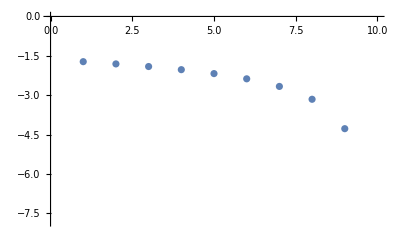

```mathematica
ListPlot[Table[{i,bphpexset[[i,1,2]]},{i,1,ncpt}]]
```

```mathematica
j1=7;k1=5;bphpshootl=100;bphpshooth=-100;scalareqex1=scalareqex/.{ym->ymset[[1]],f2->f2set[[j1]],u2->u2set[[k1]]};solex1=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==bphpshootl},bph,{x,1,xtail}];scalareqex1=scalareqex/.{ym->ymset[[1]],f2->f2set[[j1]],u2->u2set[[k1]]};solex2=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==bphpshooth},bph,{x,1,xtail}];scalareqex1=scalareqex/.{ym->ymset[[ncpt]],f2->f2set[[j1]],u2->u2set[[k1]]};solex3=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==bphpshootl},bph,{x,1,xtail}];scalareqex1=scalareqex/.{ym->ymset[[ncpt]],f2->f2set[[j1]],u2->u2set[[k1]]};solex4=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==bphpshooth},bph,{x,1,xtail}];Print[bph[x]/.solex1/.x->xtail,",",bph[x]/.solex2/.x->xtail,"\n",bph[x]/.solex3/.x->xtail,",",bph[x]/.solex4/.x->xtail]
```

{2.29142×10^191},{-2.05343×10^191}
{7.01248×10^193},{7.97737×10^193}

```mathematica
scalareqex1=scalareqex/.{ym->ymset[[ncpt]],f2->f2set[[j1]],u2->u2set[[k1]]};solex4=NDSolve[{scalareqex1==0,bph[1]==1,bph'[1]==-200},bph,{x,1,xtail}]
```

{{bph→InterpolatingFunction[{{1., 100.}}, <>]}}